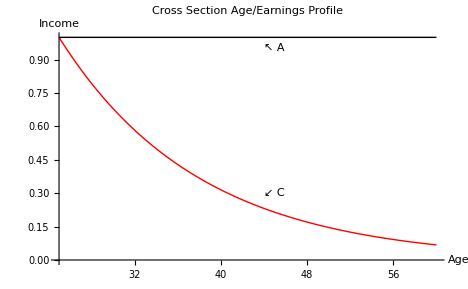

```mathematica
SetDirectory[NotebookDirectory[]];
{𝔄,ℭ} ={1.0, 1.08};
WorkStartAge = 25;
AvsCCross=Show[Plot[{𝔄^(-(Age-WorkStartAge)),ℭ^(-(Age-WorkStartAge))},{Age,WorkStartAge,60},AxesLabel->{"Age","Income"}
,PlotRange->{Automatic,{0.,Automatic}}
,PlotLabel->"Cross Section Age/Earnings Profile",PlotStyle->{Black,Red}]
,Graphics[Text["↖ A",{45,0.95}]] 
,Graphics[Text["↙ C",{45,0.3}]] 
];
Export["./AvsCCross.pdf",AvsCCross];
Show[AvsCCross]
```

```mathematica
PTime=Plot[{𝔄^(Age-WorkStartAge),ℭ^(Age-WorkStartAge)},{Age,WorkStartAge,60},AxesLabel->{"Age","Income"}
,PlotRange->{Automatic,{0.,Automatic}}
,PlotLabel->"Individual Age/Earnings Profile",PlotStyle->{Black,Red}]
```